```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
Estrai[filename_,histo_,namehisto_,nhisto_]:=Module[{file,positions,binning},
histo=.;
namehisto=.;
nhisto=.;
file=Import[filename,"Table"];
nhisto=0;
namehisto=Table[0,{j,1,100}];
positions=Table[0,{j,1,100}];
Do[
If[file[[i]]=={"<Histo>"}, 
nhisto=nhisto+1;
namehisto[[nhisto]]=file[[i+2]];
positions[[nhisto]]=i];
     ,{i,1,Length[file]}];
namehisto=Take[namehisto,nhisto];
positions=Take[positions,nhisto];
Do[(*Print[file[[ positions[[i]]+4 ]] ];*)binning[i]=file[[ positions[[i]]+4 ]];passo[i]=(binning[i][[3]]-binning[i][[2]])/binning[i][[1]],{i,1,nhisto}];
 Do[histo[i]=Table[{binning[i][[2]]+(j-1)passo[i],file[[positions[[i]]+18+j ,1 ]]},{j,0,binning[i][[1]]+1}],{i,1,nhisto}]
]
```

NOCUTS

```mathematica
(*namerun="Mtt300"*)
namerun="nocuts"
```

nocuts

```mathematica
namefolder="mupem_to_mupemttbar_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_33_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etal=prova[5];
Mll =prova[14];
Mtt =prova[15];
etat=prova[10];
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_PT},{10_ETA},{11_PT},{12_PT},{13_ETA},{14_M},{15_M},{16_M},{17_M},{18_M},{19_M},{20_DELTAR},{21_DELTAR},{22_MT_MET},{23_MT_MET}}

```mathematica
namefolder="mupem_to_mupemttbar_2to4_noQED";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalnoQED=prova[5];
MllnoQED =prova[14];
MttnoQED =prova[15];
etatnoQED=prova[10];

namefolder="mupem_to_mupemttbar_2to4_onlyVBFdiagramsandH";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalonlyVBF=prova[5];
MllonlyVBF =prova[14];
MttonlyVBF =prova[15];
etatonlyVBF=prova[10];
```

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="ZZ_ttbar_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_4_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZ =prova[10];
etatZZ=prova[6];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_4_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuhalf =prova[10];
etatZZmuhalf=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_4_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuquarter =prova[10];
etatZZmuquarter=prova[6];




NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muLePDF"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuLePDF =prova[10];
etatZZmuLePDF=prova[6];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalfLePDF"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalfLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuhalfLePDF =prova[10];
etatZZmuhalfLePDF=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterLePDF"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuquarterLePDF =prova[10];
etatZZmuquarterLePDF=prova[6];

(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZptmu =prova[10];
etatZZptmu=prova[6];*)
```

```mathematica
plotlegend0={"2to4","2to4_noQED","2to4_onlyVBF"};
plotlegend={"2to4_noQED","ttbar Eva mu=sqrtshat","ttbar Eva mu=sqrtshat/2","ttbar Eva mu=sqrtshat/4", "ttbar Eva mu=sqrtshat a la LePDF", "ttbar Eva mu=sqrtshat/2 a la LePDF", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotlegend2={"2to4_noQED", "ttbar Eva mu=sqrtshat a la LePDF", "ttbar Eva mu=sqrtshat/2 a la LePDF", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotstyle0={Thick,Thick,Thick};
plotstyle={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
plotstyle2={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="mu+ e- > t t~ at 10 TeV";
```

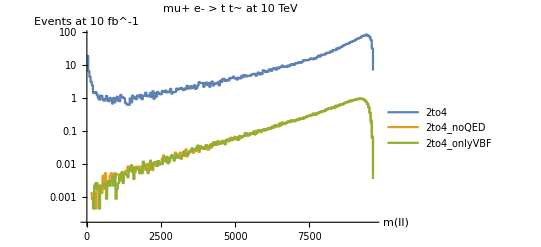

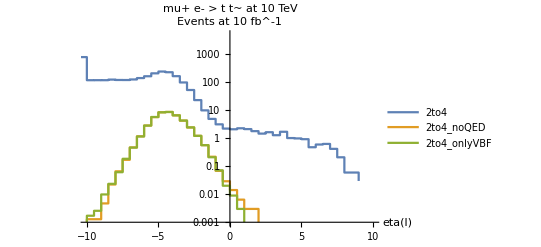

```mathematica
ListLogPlot[{joinbin[Mll,4],joinbin[MllnoQED,4],joinbin[MllonlyVBF,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend0,PlotStyle->plotstyle0,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etal,1],joinbin[etalnoQED,1],joinbin[etalonlyVBF,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend0,PlotStyle->plotstyle0,PlotRange->{{-10,10},{10^-3,5000}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

(*ListLogPlot[{joinbin[ptt,2]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,PlotRange->{{0,1000},{10,1000}},AxesLabel->{"pt(nu)","Events at 10 fb^-1"}] *)
```

```mathematica
plotlegend0={"2to4","2to4_noQED","2to4_onlyVBF"};
plotlegend={"ME-noQED","EVA mu=m(tt) with only Log[mu/MV]","EVA mu=m(tt)/2 with only Log[mu/MV]","EVA mu=m(tt)/4 with only Log[mu/MV]", "EVA mu=m(tt)", "EVA mu=m(tt)/2", "EVA mu=m(tt)/4"};
plotlegend2={"ME-noQED", "EVA mu=m(tt)", "EVA mu=m(tt)/2", "EVA mu=m(tt)/4", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotstyle0={Thick,Thick,Thick};
plotstyle={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
plotstyle2={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
```

```mathematica
plotlabel="mu+ e- > t t~ at 10 TeV, nocuts";
```

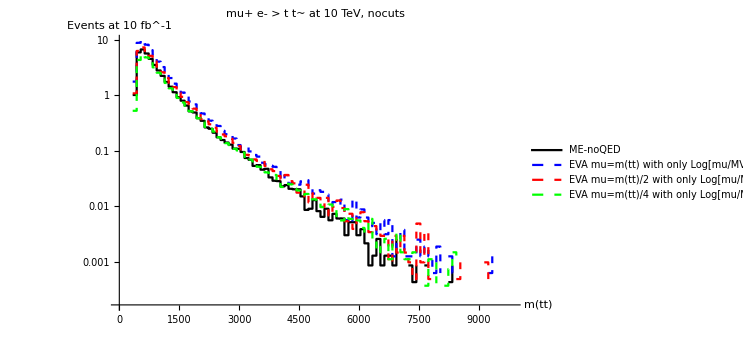

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

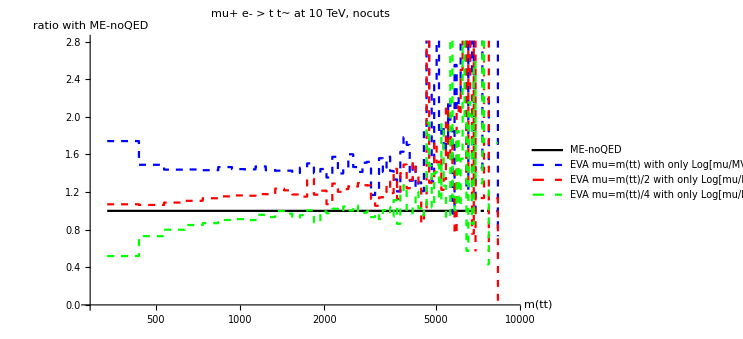

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

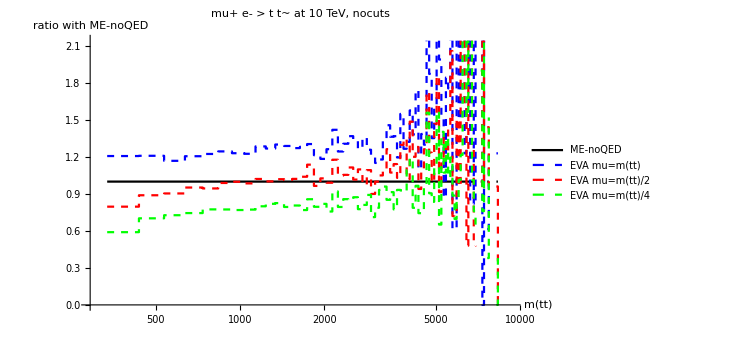

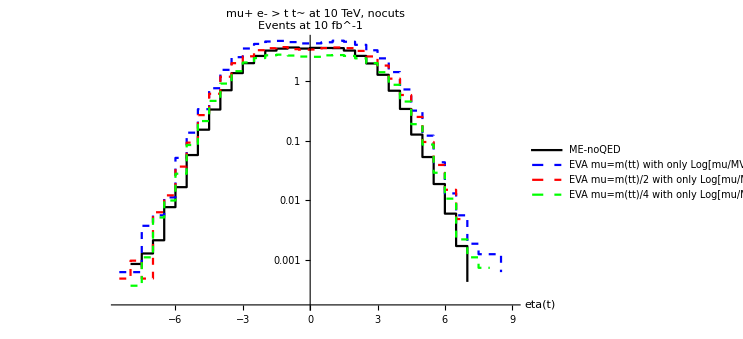

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

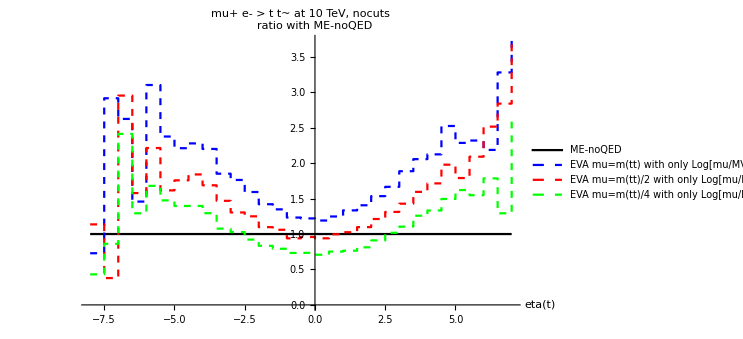

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

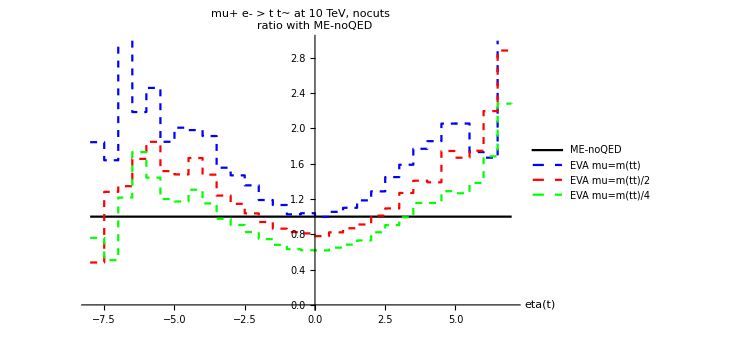

```mathematica
plotmtt=ListLogPlot[{joinbin[MttnoQED,10],joinbin[MttZZ,10],joinbin[MttZZmuhalf,10],joinbin[MttZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(tt)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmttratio1=ListLogLinearPlot[{rapp[joinbin[MttnoQED,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZ,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuhalf,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuquarter,10],joinbin[MttnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(tt)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmttratio2=ListLogLinearPlot[{rapp[joinbin[MttnoQED,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuLePDF,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuhalfLePDF,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuquarterLePDF,10],joinbin[MttnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(tt)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 





plotetat=ListLogPlot[{etatnoQED,etatZZ,etatZZmuhalf,etatZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(t)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotetatratio1=ListPlot[{rapp[joinbin[etatnoQED,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZ,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuhalf,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuquarter,1],joinbin[etatnoQED,1]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(t)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotetatratio2=ListPlot[{rapp[joinbin[etatnoQED,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuLePDF,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuhalfLePDF,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuquarterLePDF,1],joinbin[etatnoQED,1]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"eta(t)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 
dir="/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotDistr/ZZ_tt/";
run="10TeVnocuts/";
Export[dir<>run<>"plotmtt.pdf",plotmtt];
Export[dir<>run<>"plotmttratio1.pdf",plotmttratio1];
Export[dir<>run<>"plotmttratio2.pdf",plotmttratio2];
Export[dir<>run<>"plotetat.pdf",plotetat];
Export[dir<>run<>"plotetatratio1.pdf",plotetatratio1];
Export[dir<>run<>"plotetatratio2.pdf",plotetatratio2];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

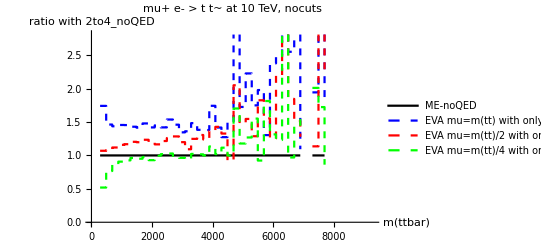

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

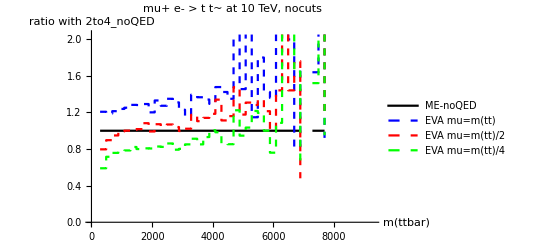

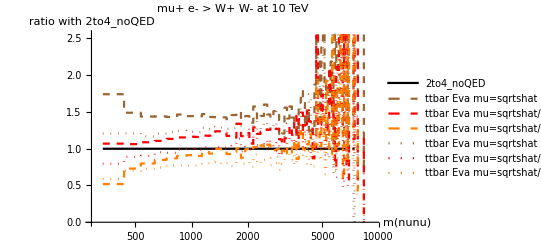

```mathematica
rebinning=20;
ListPlot[{rapp[joinbin[MttnoQED,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZ,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuhalf,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuquarter,rebinning],joinbin[MttnoQED,rebinning]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_noQED"}] 

ListPlot[{rapp[joinbin[MttnoQED,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuLePDF,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuhalfLePDF,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuquarterLePDF,rebinning],joinbin[MttnoQED,rebinning]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_noQED"}]
```

M(ttbar)>500 GeV con anche Pt(t)> 150 GeV e |etat|<2.5.

```mathematica
(*namerun="Mtt300"*)
namerun="Mtt500_ptt150_eta2half"
```

Mtt500_ptt150_eta2half

```mathematica
namefolder="mupem_to_mupemttbar_2to4";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_33_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etal=prova[5];
Mll =prova[14];
Mtt =prova[15];
etat=prova[10];
```

Import::nffil: File /Users/pagani/mu-vbf/Davide2025/mupem_to_mupemttbar_2to4/HTML/Mtt500_ptt150_eta2half/tag_33_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_Mtt500_ptt150_eta2half/MadAnalysis5job_0/Histograms/histos.saf not found during Import.

```mathematica
NameH
```

{}

```mathematica
namefolder="mupem_to_mupemttbar_2to4_noQED";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalnoQED=prova[5];
MllnoQED =prova[14];
MttnoQED =prova[15];
etatnoQED=prova[10];

namefolder="mupem_to_mupemttbar_2to4_onlyVBFdiagramsandH";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalonlyVBF=prova[5];
MllonlyVBF =prova[14];
MttonlyVBF =prova[15];
etatonlyVBF=prova[10];
```

```mathematica
(*namerun="test180"*)
```

```mathematica
namefolder="ZZ_ttbar_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_5_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZ =prova[10];
etatZZ=prova[6];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_5_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuhalf =prova[10];
etatZZmuhalf=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_5_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuquarter =prova[10];
etatZZmuquarter=prova[6];




NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muLePDF"<>"/tag_5_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuLePDF =prova[10];
etatZZmuLePDF=prova[6];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalfLePDF"<>"/tag_5_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalfLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuhalfLePDF =prova[10];
etatZZmuhalfLePDF=prova[6];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterLePDF"<>"/tag_5_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuquarterLePDF =prova[10];
etatZZmuquarterLePDF=prova[6];

(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZptmu =prova[10];
etatZZptmu=prova[6];*)
```

```mathematica
plotlegend0={"2to4","2to4_noQED","2to4_onlyVBF"};
plotlegend={"2to4_noQED","ttbar Eva mu=sqrtshat","ttbar Eva mu=sqrtshat/2","ttbar Eva mu=sqrtshat/4", "ttbar Eva mu=sqrtshat a la LePDF", "ttbar Eva mu=sqrtshat/2 a la LePDF", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotlegend2={"2to4_noQED", "ttbar Eva mu=sqrtshat a la LePDF", "ttbar Eva mu=sqrtshat/2 a la LePDF", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotstyle0={Thick,Thick,Thick};
plotstyle={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
plotstyle2={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="mu+ e- > t t~ at 10 TeV";
```

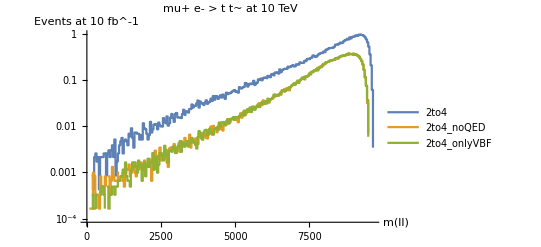

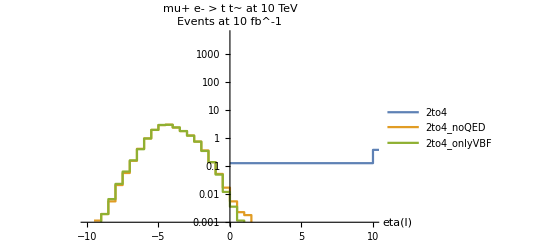

```mathematica
ListLogPlot[{joinbin[Mll,4],joinbin[MllnoQED,4],joinbin[MllonlyVBF,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend0,PlotStyle->plotstyle0,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etal,1],joinbin[etalnoQED,1],joinbin[etalonlyVBF,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend0,PlotStyle->plotstyle0,PlotRange->{{-10,10},{10^-3,5000}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

(*ListLogPlot[{joinbin[ptt,2]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,PlotRange->{{0,1000},{10,1000}},AxesLabel->{"pt(nu)","Events at 10 fb^-1"}] *)
```

```mathematica
plotlegend0={"2to4","2to4_noQED","2to4_onlyVBF"};
plotlegend={"ME-noQED","EVA mu=m(tt) with only Log[mu/MV]","EVA mu=m(tt)/2 with only Log[mu/MV]","EVA mu=m(tt)/4 with only Log[mu/MV]", "EVA mu=m(tt)", "EVA mu=m(tt)/2", "EVA mu=m(tt)/4"};
plotlegend2={"ME-noQED", "EVA mu=m(tt)", "EVA mu=m(tt)/2", "EVA mu=m(tt)/4", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotstyle0={Thick,Thick,Thick};
plotstyle={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
plotstyle2={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
```

```mathematica
plotlabel="mu+ e- > t t~ at 10 TeV, M(tt)>500 GeV, Pt(t)> 150 GeV,  |etat|<2.5";
```

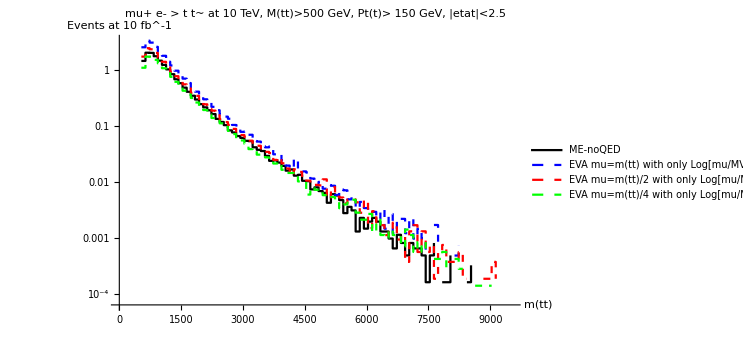

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

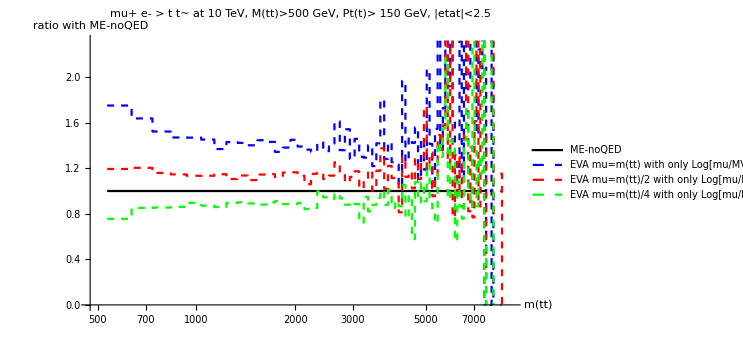

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

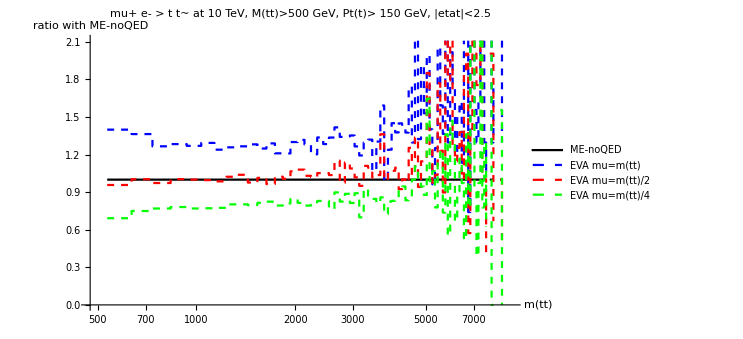

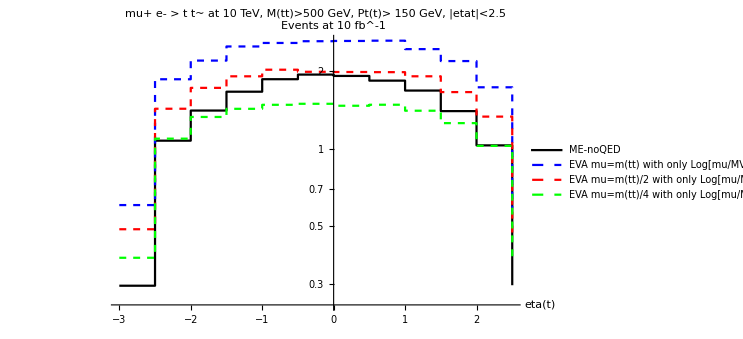

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

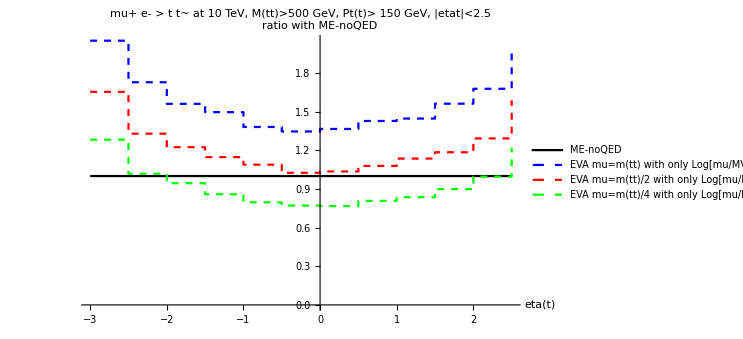

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

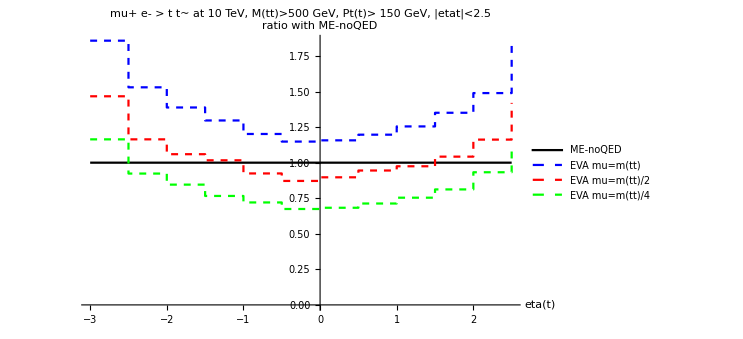

```mathematica
plotmtt=ListLogPlot[{joinbin[MttnoQED,10],joinbin[MttZZ,10],joinbin[MttZZmuhalf,10],joinbin[MttZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(tt)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmttratio1=ListLogLinearPlot[{rapp[joinbin[MttnoQED,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZ,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuhalf,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuquarter,10],joinbin[MttnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(tt)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmttratio2=ListLogLinearPlot[{rapp[joinbin[MttnoQED,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuLePDF,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuhalfLePDF,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuquarterLePDF,10],joinbin[MttnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(tt)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 





plotetat=ListLogPlot[{etatnoQED,etatZZ,etatZZmuhalf,etatZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(t)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotetatratio1=ListPlot[{rapp[joinbin[etatnoQED,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZ,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuhalf,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuquarter,1],joinbin[etatnoQED,1]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(t)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotetatratio2=ListPlot[{rapp[joinbin[etatnoQED,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuLePDF,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuhalfLePDF,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuquarterLePDF,1],joinbin[etatnoQED,1]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"eta(t)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 
dir="/Users/pagani/mu-vbf/Davide2025/Notebooks/PlotDistr/ZZ_tt/";
run="10TeVcuts/";
Export[dir<>run<>"plotmtt.pdf",plotmtt];
Export[dir<>run<>"plotmttratio1.pdf",plotmttratio1];
Export[dir<>run<>"plotmttratio2.pdf",plotmttratio2];
Export[dir<>run<>"plotetat.pdf",plotetat];
Export[dir<>run<>"plotetatratio1.pdf",plotetatratio1];
Export[dir<>run<>"plotetatratio2.pdf",plotetatratio2];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

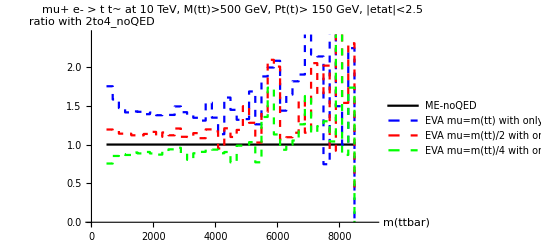

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

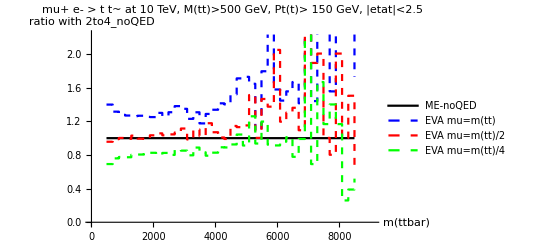

```mathematica
rebinning=20;
ListPlot[{rapp[joinbin[MttnoQED,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZ,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuhalf,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuquarter,rebinning],joinbin[MttnoQED,rebinning]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_noQED"}] 

ListPlot[{rapp[joinbin[MttnoQED,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuLePDF,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuhalfLePDF,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuquarterLePDF,rebinning],joinbin[MttnoQED,rebinning]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_noQED"}]
```